```mathematica
LinearSpline1[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]
```

```mathematica
LinearSpline2[points_][x_]:=With[{p=Sort[points]},

]
```

```mathematica
p=RandomReal[{0, 1}, {10, 2}];
```

```mathematica
RepeatedTiming[LinearSpline1[p][RandomReal[]]]
RepeatedTiming[LinearSpline2[p][RandomReal[]]]
```

{0.0000653569,0.0928845}

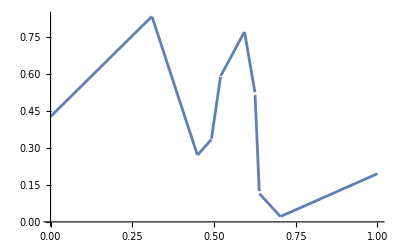

```mathematica
Plot[LinearSpline1[p][x], {x, 0, 1}]
```